```mathematica
data=Import["D:\\Documents\\SocialNetwork\\NN\\NN.txt"];
```

```mathematica
data=StringSplit[data];
```

```mathematica
Length[data]/3
```

2345

```mathematica
a=Table[ToExpression[data[[3*i-2]]],{i,1,2345}];
b=Table[ToExpression[data[[3*i-1]]],{i,1,2345}];
c=Table[ToExpression[data[[3*i]]],{i,1,2345}];
```

```mathematica
rule=Table[a[[i]]-> b[[i]],{i,1,2345}];
```

```mathematica
dist=Table[1/c[[i]],{i,1,2345}];
```

```mathematica
d=Graph[rule,EdgeWeight->c]
```

-Graphics-

```mathematica
CommunityGraphPlot[d,Method->"SpringElectrical"]
```

-Graphics-

```mathematica
sub=FindGraphCommunities[d,Method->"Modularity"]
```

{{1,90,92,69,89,91,3,9,17,21,93,94,23,121,125,131,31,4,10,16,18,22,24,97,122,126,132,32,5,7,101,6,102,99,100,27,8,26,44,37,11,19,29,12,41,118,30,13,143,28,43,14,20,34,15,40,139,140,108,35,107,133,134,105,106,36,33,161,129,120,38,160,130,70,98},{305,189,225,226,227,228,229,230,234,235,236,237,238,239,240,242,251,252,253,254,255,256,276,241,165,169,168,153,151,277,152,245,278,167,269,270,258,274,191,244,260,261,262,263,264,265,266,282,279,231,280,232,281,233,246,247,248,243,257,259,267,268,271,273,291,292,293,294,295,296,297,298,299,300},{51,113,47,60,303,25,128,136,135,39,45,55,119,137,46,114,56,62,86,138,109,52,58,61,85,48,110,88,49,54,50,96,127,95,166,53,57,63,87,84,59,67,178,64,65,220,66,68,221,111,112,177,83,103,104,214,213,201,202,272,211},{72,77,78,71,144,73,74,174,42,82,141,142,193,75,76,81,80,216,154,146,150,203,217,162,164,249,250,204,163,117,215,79,148,145,147,192,219,157,172,218,156,170,224,155,173,149,205,206,184,171,185,181,182,194,207,223,208},{2,158,159,222,198,179,180,306,200,199,124,115,123,183,116,175,176,209,212,301,302},{186,187,188,195,197,196,275,190,210}}

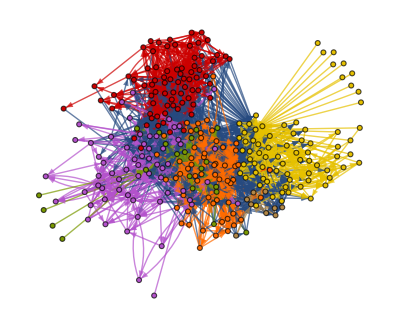

```mathematica
HighlightGraph[d,Map[Subgraph[d,#]&,%]]
```

```mathematica
Length[sub]
```

6

```mathematica
g1=Subgraph[d,sub[[1]]]
```

-Graphics-

```mathematica
g2=Subgraph[d,sub[[2]]]
```

-Graphics-

```mathematica
g3=Subgraph[d,sub[[3]]]
```

-Graphics-

```mathematica
g4=Subgraph[d,sub[[4]]]
```

-Graphics-

```mathematica
g5=Subgraph[d,sub[[5]]]
```

-Graphics-

```mathematica
g6=Subgraph[d,sub[[6]]]
```

-Graphics-

```mathematica
degree[x_]:=Module[
{x0=0,x1=0,x2=0,x3=0,x4=0,x5=0,x6=0,i},
{
For[
i=1,
i≤Length[x],
i++,
{
If[
x[[i]]≥32,
x6++,
{
If[
x[[i]]≥16,
x5++,
{
If[
x[[i]]≥8,
x4++,
{
If[
x[[i]]≥4,
x3++,
{
If[
x[[i]]≥2,
x2++,
{
If[
x[[i]]≥1,
x1++,
x0++
]
}
]
}
]
}
]
}
]
}
]
}
];
{x0,x1,x2,x3,x4,x5,x6}
}
]
```

```mathematica
l1=degree[VertexDegree[g1]]
```

{{0,1,4,17,37,15,1}}

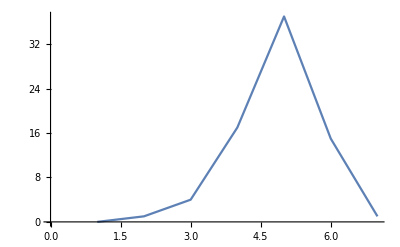

```mathematica
ListPlot[l1,Joined->True]
```

```mathematica
l2=degree[VertexDegree[g2]]
```

{{0,10,11,28,23,1,1}}

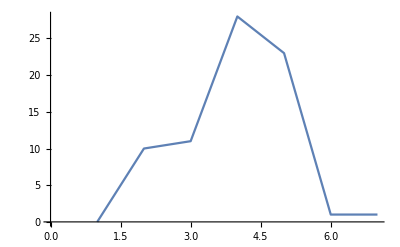

```mathematica
ListPlot[l2,Joined->True]
```

```mathematica
l3=degree[VertexDegree[g3]]
```

{{0,1,7,24,21,8,0}}

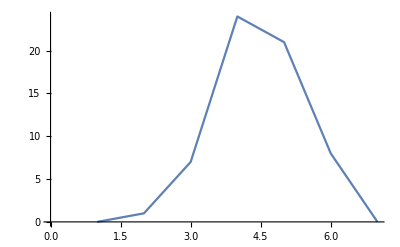

```mathematica
ListPlot[l3,Joined->True]
```

```mathematica
l4=degree[VertexDegree[g4]]
```

{{0,0,2,14,24,12,5}}

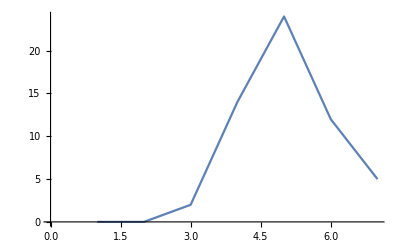

```mathematica
ListPlot[l4,Joined->True]
```

```mathematica
l5=degree[VertexDegree[g5]]
```

{{0,5,2,5,9,0,0}}

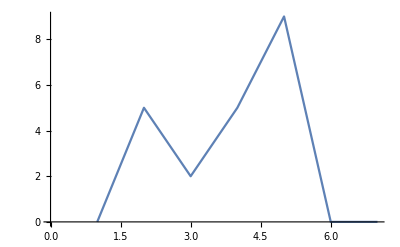

```mathematica
ListPlot[l5,Joined->True]
```

```mathematica
l6=degree[VertexDegree[g6]]
```

{{0,1,3,4,1,0,0}}

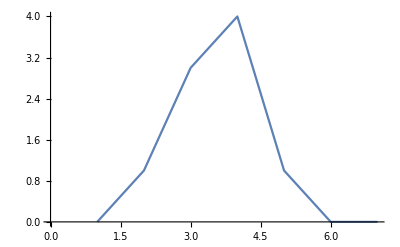

```mathematica
ListPlot[l6,Joined->True]
```

```mathematica
l=degree[VertexDegree[d]]
```

{{0,15,7,43,127,82,23}}

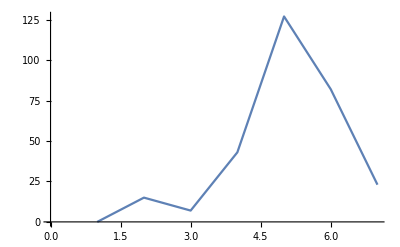

```mathematica
ListPlot[l,Joined->True]
```

```mathematica
gg=Graph[d,EdgeWeight->dist]
```

-Graphics-

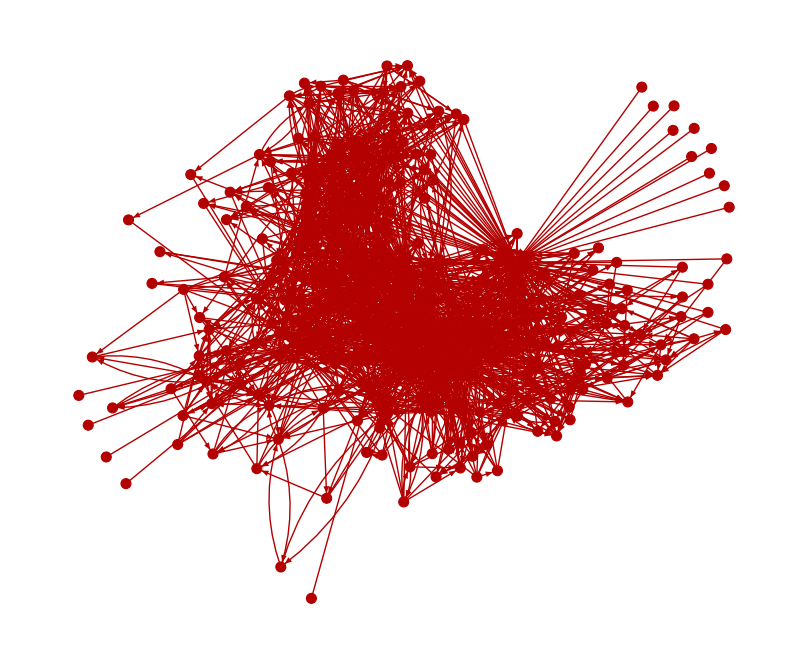

```mathematica
HighlightGraph[d,Map[Subgraph[d,#]&,%]]
```

```mathematica
FindClique[d,{2,Infinity},All]
```

{{149,205,206},{219,218,149},{48,110,88},{81,178,157},{109,67,111},{174,219,218},{144,154,155},{222,217,180},{222,198,180},{89,99,100},{89,108,98},{89,139,108},{71,75,203},{72,76,204},{90,139,108},{90,99,100},{207,208},{181,182},{272,271},{224,223},{170,184},{99,123},{115,183},{219,173},{147,149},{145,192},{168,153},{148,147},{169,167},{165,168},{215,219},{200,199},{177,147},{276,167},{117,148},{195,196},{195,197},{250,195},{217,224},{217,145},{179,183},{179,180},{238,247},{236,246},{235,245},{227,169},{227,276},{68,112},{65,220},{178,270},{178,269},{178,177},{178,221},{67,65},{198,145},{166,165},{95,104},{95,103},{96,115},{96,104},{96,103},{49,54},{216,223},{216,217},{216,179},{216,198},{80,192},{80,147},{80,79},{48,80},{81,219},{81,148},{81,216},{81,80},{76,215},{76,217},{75,216},{75,76},{58,84},{58,50},{58,110},{52,166},{109,177},{109,59},{109,58},{193,79},{193,117},{56,110},{114,84},{142,96},{46,193},{46,86},{46,62},{46,114},{119,198},{55,198},{55,63},{55,109},{45,55},{82,218},{82,172},{82,147},{82,79},{189,187},{174,171},{174,178},{160,170},{120,95},{120,96},{161,62},{73,74},{128,95},{40,160},{40,120},{40,33},{14,34},{143,173},{143,154},{13,143},{118,55},{118,14},{41,34},{44,70},{5,222},{5,7},{126,160},{122,101},{22,118},{18,14},{18,41},{18,99},{16,22},{10,16},{4,18},{121,102},{21,15},{21,118},{17,128},{17,40},{9,37},{3,17},{91,52},{89,107},{89,140},{89,97},{71,217},{71,47},{69,91},{113,83},{113,87},{113,88},{158,200},{92,118},{2,158},{78,217},{77,216},{77,71},{72,216},{72,144},{72,71},{72,78},{51,127},{51,96},{51,154},{51,58},{51,92},{90,107},{90,140},{90,101},{90,97}}

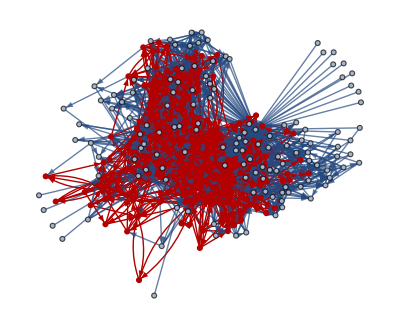

```mathematica
HighlightGraph[d,Subgraph[d,%]]
```

```mathematica
label=Table[-1,{i,1,306}];
```

```mathematica
For[
i=1,
i≤Length[sub],
i++,
{
For[
j=1,
j≤Length[sub[[i]]],
j++,
label[[sub[[i]][[j]]]]=i
]
}
]
```

```mathematica
FindKClan[d,2]
```

{{72,77,71,75,76,216,203,217,204,215,223}}

```mathematica
{{72,77,71,75,76,216,203,217,204,215,223}}(*All belong to label 4*)
```

```mathematica
label
```

{1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,4,1,1,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,3,1,1,1,1,1,1,3,3,1,1,1,1,1,1,3,3,1,1,1,1,3,3,3,3,3,3,5,5,4,1,3,1,1,1,5,5,1,1,3,3,1,1,1,1,1,1,3,3,3,3,1,1,4,4,1,4,4,4,4,4,4,4,2,2,2,4,4,4,4,5,5,1,1,4,4,4,2,3,2,2,2,4,4,4,4,4,5,5,3,3,5,5,4,4,5,4,4,6,6,6,2,6,2,4,4,4,6,6,6,5,5,5,3,3,4,4,4,4,4,4,5,6,3,5,3,3,4,4,4,4,4,3,3,5,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,6,2,2,2,2,2,2,2,-1,-1,-1,-1,-1,-1,-1,-1,2,2,2,2,2,2,2,2,2,2,5,5,3,-1,2,5}

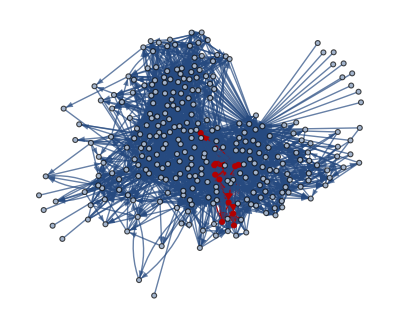

```mathematica
HighlightGraph[d,Subgraph[d,%]]
```

```mathematica
KCoreComponents[d,10]
```

{{1,51,72,77,78,2,90,92,158,159,71,89,91,47,17,93,94,121,18,122,222,101,305,99,100,8,44,41,118,143,144,40,128,139,140,108,107,73,136,74,161,120,38,160,174,82,141,55,119,46,142,56,62,193,52,61,75,76,81,48,80,216,154,96,127,95,166,198,178,220,221,111,146,227,228,229,150,234,235,236,237,240,217,162,251,252,253,117,276,306,177,200,199,169,79,148,168,145,147,192,219,157,172,218,98,124,115,123,156,170,116,153,155,173,149,277,152,245,270}}

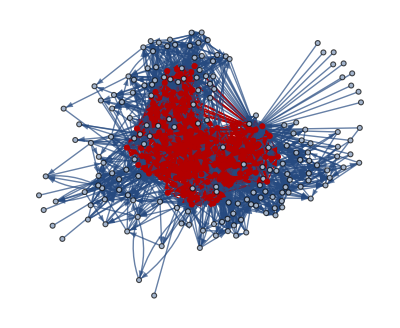

```mathematica
HighlightGraph[d,Subgraph[d,%]]
```

```mathematica
N[GraphAssortativity[d]]
```

0.212372

```mathematica
dCore=Subgraph[d,KCoreComponents[d,10]]
```

-Graphics-

```mathematica
N[GraphAssortativity[dCore]]
```

0.180697

```mathematica
cent=DegreeCentrality[dCore]
```

{10,22,51,43,45,11,32,15,19,15,51,28,17,12,14,12,12,12,16,12,15,13,48,20,21,10,11,14,16,21,22,14,15,18,15,18,14,46,10,46,18,25,10,17,16,29,13,13,17,12,13,15,17,25,26,11,36,39,32,14,21,35,17,31,11,25,16,28,29,15,15,12,14,13,10,11,12,14,13,11,10,13,35,12,13,14,10,23,17,11,21,21,21,13,20,18,13,21,18,21,27,17,12,25,13,10,19,13,11,11,19,16,18,13,22,12,11,14,13}

```mathematica
HighlightGraph[dCore,VertexList[dCore],VertexSize-> Thread[VertexList[dCore]-> Rescale[%]]]
```

-Graphics-

```mathematica
degree[cent]
```

{{0,0,0,0,60,46,13}}

```mathematica
ug=Graph[rule]
```

-Graphics-

```mathematica
Length[KCoreComponents[ug,10][[1]]]
```

119

```mathematica
HighlightGraph[ug,Subgraph[ug,%]]
```

-Graphics-

```mathematica
KC=Table[Length[KCoreComponents[ug,i][[1]]],{i,1,11}]
```

Part::partw: Part 1 of {} does not exist.

{297,282,278,274,265,251,236,202,166,119,2}

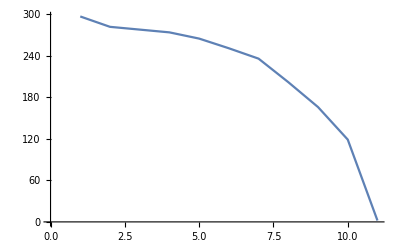

```mathematica
ListPlot[KC,Joined->True]
```

```mathematica
sg=Subgraph[d,KCoreComponents[d,10]]
```

-Graphics-